# Homework 3

## Section I: Synthesis Problem #1

### 1.1. Find optimal time

```mathematica
Clear[μ,ν,x1,x2,θ]
μ=-3;ν=6;
x1=0.5;x2=0.5;
s=NSolve[{2μ θ-1+Exp[-2μ θ]==2 μ^2(x1^2+x2^2)&&θ>=0},θ];
T=s[[1]][[1]][[2]];
Print["Optimal time is ",T]
```

Optimal time is 0.421327

### 1.2. Find function θ(x_1,x_2)

Since solving the equation explicitly is fairly difficult, we do the following instead:
1. Define the grid of values of {x_1^(i),x_2^(i)}_i.
2. Interpolate the polynomial through this set of points.

```mathematica
Clear[x1,x2]
t=Table[
{x1,x2,NSolve[{2μ θ-1+Exp[-2μ θ]==2 μ^2(x1^2+x2^2)&&θ>=0},θ][[1]][[1]][[2]]},
{x1,-0.6,0.6,0.02},
{x2,-0.6,0.6,0.02}
];
```

```mathematica
ListPointPlot3D[t,
PlotTheme->"Detailed",
PlotStyle->Directive[PointSize[0.01]],
ImageSize->550]
```

-Graphics3D-

Now, flatten the array and conduct the interpolation operation.

```mathematica
ft=Flatten[t];
θ[x1_,x2_]=Interpolation[Table[{{ft[[i]],ft[[i+1]]},ft[[i+2]]},{i,1,Length[ft],3}],{x1,x2}];
Show[
Plot3D[θ[x1,x2],{x1,-0.5,0.5},{x2,-0.5,0.5},PlotTheme->"Detailed",PlotStyle->Directive[Purple,Opacity[0.5]]],
ListPointPlot3D[t,PlotStyle->Directive[PointSize[0.01]]],
ImageSize->550
]
```

-Graphics3D-

### 1.3. Find the trajectory

First, define the controlling function

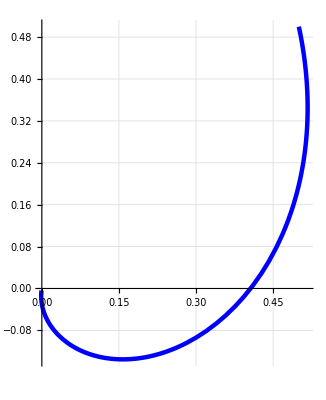

```mathematica
Clear[x1,x2,t]
u1[x1_,x2_]=-θ[x1,x2] x1/(x1^2+x2^2);
u2[x1_,x2_]=-θ[x1,x2] x2/(x1^2+x2^2);
s=NDSolve[{x1'[t]==μ x1[t]+ν x2[t]+u1[x1[t],x2[t]],
x2'[t]==-ν x1[t]+μ x2[t]+u2[x1[t],x2[t]],
x1[0]==0.5,x2[0]==0.5},
{x1[t],x2[t]},{t,T}];
Show[
ParametricPlot[Evaluate[{x1[t],x2[t]}/.s],{t,0,T},
GridLines->Automatic,
PlotStyle->Directive[Blue,Thickness[0.008]]]
]
```

Additionally, building the control functions u_1(t) and u_2(t)

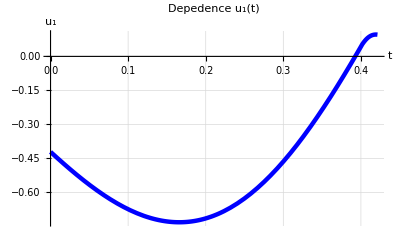

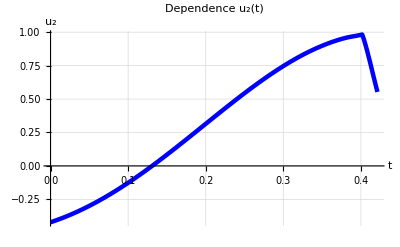

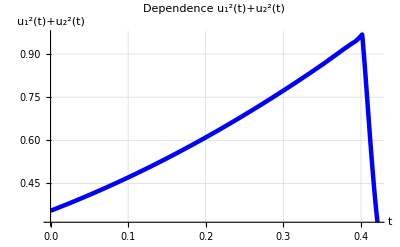

```mathematica
Show[
Plot[Evaluate[u1[x1[t],x2[t]]/.s],{t,0,T},
GridLines->Automatic,
PlotStyle->Directive[Blue,Thickness[0.008]]],
PlotLabel->"Depedence u_1(t)",
AxesLabel->{"t","u_1"}
]
Show[
Plot[Evaluate[u2[x1[t],x2[t]]/.s],{t,0,T},
GridLines->Automatic,
PlotStyle->Directive[Blue,Thickness[0.008]]],
PlotLabel->"Dependence u_2(t)",
AxesLabel->{"t","u_2"}
]
Show[
Plot[Evaluate[{u1[x1[t],x2[t]]^2+u2[x1[t],x2[t]]^2}/.s],{t,0,T},
GridLines->Automatic,
PlotStyle->Directive[Blue,Thickness[0.008]]],
PlotLabel->"Dependence u_1^2(t)+u_2^2(t)",
AxesLabel->{"t","u_1^2(t)+u_2^2(t)"}
]
```

Notice: Notice that indeed u_1^2+u_2^2<=1 for all t.

## Section II: Synthesis Problem #2

### 2.1. Region plotting

We need to plot the region 3 x_1^2+2 x_1 x_2+x_2^2<=2/9 and pick a random point inside.

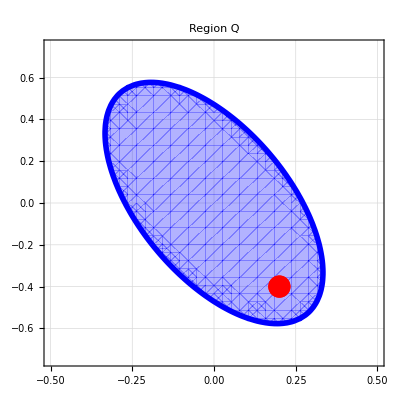

```mathematica
x10=0.2;x20=-0.4;
Show[
RegionPlot[{3 x1^2+2x1 x2+x2^2<=2/9},{x1,-0.5,0.5},{x2,-0.75,0.75},
GridLines->Automatic,
PlotStyle->Directive[Blue,Opacity[0.3]],
BoundaryStyle->Directive[Blue,Thickness[0.01]]],
ListPlot[{{x10,x20}},PlotStyle->Directive[Red,PointSize[0.04]]],
PlotLabel->"Region Q"
]
```

### 2.2. Finding θ at given point

```mathematica
s=NSolve[{2/9 θ^4-θ^2 x20^2-2θ x10 x20-3 x10^2==0,θ>=0},θ];
θ0=s[[1]][[1]][[2]];
Print["The value of θ at given point is ",θ0]
```

The value of θ at given point is 0.80924

### 2.3. Solving Differential Equation

Note: We adjust the parameter T to make the destination point at distance less than 0.01 to the center. Solve the equation first.

```mathematica
Clear[t]
ϵ=0.005;δ=0.01;T=1.74;
s=NDSolve[{x1'[t]==x2[t]+ϵ((-x1[t]^2)/x3[t]^2-(2x1[t] x2[t])/x3[t]+x2[t]^2),
x2'[t]==-x1[t]/x3[t]^2-(2x2[t])/x3[t]+δ((x1[t]x2[t])/x3[t]^2+(2 x2[t]^2)/x3[t]+x1[t]^2),
x3'[t]==- (x1[t]^2+x2[t]^2 x3[t]^2)/(6 x1[t]^2+3x1[t]x2[t]x3[t]+x3[t]^2 x2[t]^2)+ ((-3+x3[t]^3)x1[t]^3+x3[t](-8+x3[t]^3)x1[t]^2 x2[t]-2 x3[t]^2 x1[t] x2[t]^2-x3[t]^3 x2[t]^3)/(100x3[t](6 x1[t]^2+3x1[t]x2[t]x3[t]+x3[t]^2 x2[t]^2)),
x1[0]==x10,x2[0]==x20,x3[0]==θ0},{x1[t],x2[t],x3[t]},{t,T}];
Evaluate[{x1[t]^2+x2[t]^2<=0.01^2}/.s]/.{t->T}
```

{{True}}

Now, building the trajectory

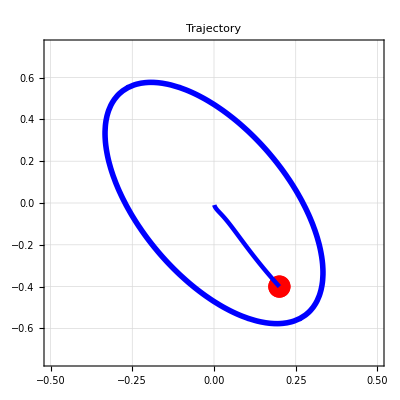

```mathematica
Show[
RegionPlot[{3 x1^2+2x1 x2+x2^2<=2/9},{x1,-0.5,0.5},{x2,-0.75,0.75},
GridLines->Automatic,
PlotStyle->Directive[Opacity[0.0]],
BoundaryStyle->Directive[Blue,Thickness[0.01]]],
ListPlot[{{x10,x20}},PlotStyle->Directive[Red,PointSize[0.04]]],
ParametricPlot[Evaluate[{x1[t],x2[t]}/.s],{t,0,T},
GridLines->Automatic,
PlotStyle->Directive[Blue,Thickness[0.008]]],
PlotLabel->"Trajectory"
]
```

Plot the control function and controlability derivative:

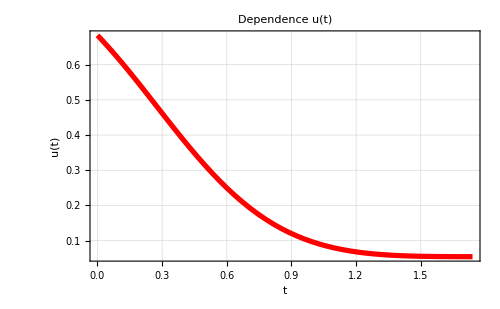

```mathematica
Plot[Evaluate[(-x1[t]/x3[t]^2-2x2[t]/x3[t])/.s],
{t,0.0,T},PlotRange->All,PlotTheme->"Scientific",
PlotStyle->Directive[Red,Thickness[0.0075]],GridLines->Automatic,
ImageSize->500,PlotLabel->"Dependence u(t)",AxesLabel->{"t","u(t)"}]
```

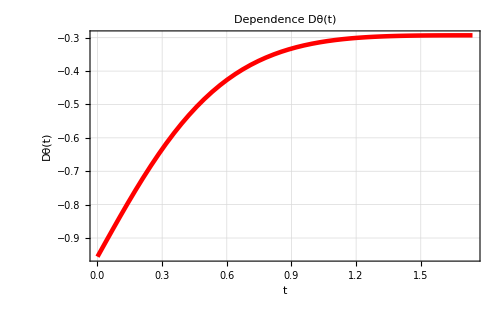

```mathematica
θd[x1_,x2_,x3_]=- (x1^2+x2^2 x3^2)/(6 x1^2+3x1 x2 x3+x3^2 x2^2)+ ((-3+x3^3)x1^3+x3(-8+x3^3)x1^2 x2-2 x3^2 x1 x2^2-x3^3 x2^3)/(100x3(6 x1^2+3x1 x2 x3+x3^2 x2^2));
Plot[Evaluate[θd[x1[t],x2[t],x3[t]]/.s],
{t,0.0,T},PlotRange->All,PlotTheme->"Scientific",
PlotStyle->Directive[Red,Thickness[0.0065]],GridLines->Automatic,
ImageSize->500,PlotLabel->"Dependence Dθ(t)",AxesLabel->{"t","Dθ(t)"}]
```

### 2.4. Trajectory, Control Function, Derivative

Since I am not totally sure about the trajectory and control function from the last subsection, I decided to do everything from scratch, using control function u(x)=-x_1/(θ^2(x_1,x_2))-(2 x_2)/(θ(x_1,x_2)).
First, approximating the function θ(x_1,x_2), as with the first question.

```mathematica
Clear[x1,x2]
tab=Table[
{x1,x2,NSolve[{2/9 θ^4-x2^2 θ^2-2θ x1 x2-3 x1^2==0&&θ>=0},θ][[1]][[1]][[2]]},
{x1,-0.8,0.8,0.041},
{x2,-0.8,0.8,0.041}
];
```

```mathematica
ListPointPlot3D[tab,
PlotTheme->"Detailed",
PlotStyle->Directive[PointSize[0.01]],
ImageSize->600]
```

-Graphics3D-

```mathematica
ft=Flatten[tab];
θ[x1_,x2_]=Interpolation[Table[{{ft[[i]],ft[[i+1]]},ft[[i+2]]},{i,1,Length[ft],3}],{x1,x2}];
Show[
Plot3D[θ[x1,x2],{x1,-0.8,0.8},{x2,-0.8,0.8},PlotTheme->"Detailed",PlotStyle->Directive[Purple,Opacity[0.5]]],
ListPointPlot3D[tab,PlotStyle->Directive[PointSize[0.01]]],
ImageSize->600
]
```

-Graphics3D-

Solving the differential equation!

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

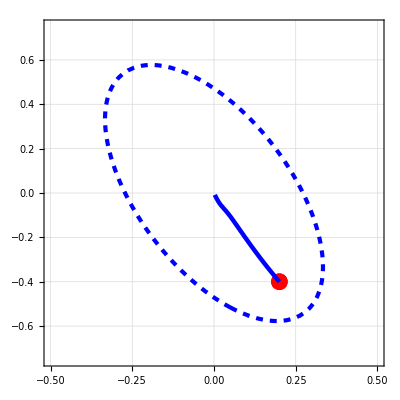

```mathematica
u[x1_,x2_]=-x1/θ[x1,x2]^2-(2x2)/θ[x1,x2];
s=NDSolve[{x1'[t]==x2[t]+ϵ(x2[t]^2+x1[t]u[x1[t],x2[t]]),
x2'[t]==u[x1[t],x2[t]]+δ(x1[t]^2-x2[t]u[x1[t],x2[t]]),
x1[0]==x10,x2[0]==x20},{x1,x2},{t,T}]
Show[
RegionPlot[{3 x1^2+2x1 x2+x2^2<=2/9},{x1,-0.5,0.5},{x2,-0.75,0.75},
GridLines->Automatic,
PlotStyle->Directive[Opacity[0.0]],
BoundaryStyle->Directive[Blue,Thickness[0.0075],Dashed]],
ListPlot[{{x10,x20}},PlotStyle->Directive[Red,PointSize[0.03]]],
ParametricPlot[Evaluate[{x1[t],x2[t]}/.s],{t,0,T},
GridLines->Automatic,
PlotStyle->Directive[Blue,Thickness[0.008]]]
]
```

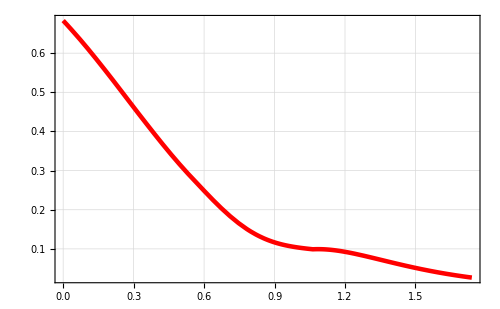

```mathematica
Plot[Evaluate[u[x1[t],x2[t]]/.s],
{t,0.0,T},PlotRange->All,PlotTheme->"Scientific",
PlotStyle->Directive[Red,Thickness[0.0065]],GridLines->Automatic,
ImageSize->500]
```

Controlability Function Derivative

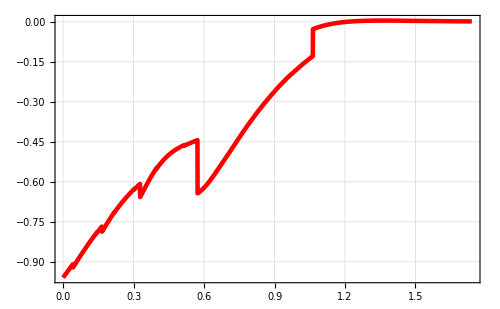

```mathematica
Plot[Evaluate[{D[θ[x1[t],x2[t]],t]}/.s],
{t,0.0,T},PlotRange->All,PlotTheme->"Scientific",
PlotStyle->Directive[Red,Thickness[0.0065]],GridLines->Automatic,
ImageSize->500]
```